```mathematica
image=Import["C:\\Users\\97587\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\Images\\TrainingData_21.jpg"]
{r,g,b} = ColorSeparate[image]
points = ComponentMeasurements[ContourDetect[MinDetect[r-g, 0.08]], "Centroid"][[All, 2]]
HighlightImage[image,points]
```

```mathematica
-Graphics-//ImageDimensions
```

{360,259}

```mathematica
ImageResize[-Graphics-,{360,240}]
```

-Graphics-

```mathematica
axes = 1-ContourDetect[MinDetect[image, 0.5]]
```

-Graphics-

```mathematica
lines = ImageLines[axes, 0.2,MaxFeatures->2]
{xAxis,yAxis}=lines
HighlightImage[image, lines]
```

{Line[{{0.,34.1803},{360.,34.1803}}],Line[{{15.8599,259.},{15.0347,0.}}]}

{Line[{{0.,34.1803},{360.,34.1803}}],Line[{{15.8599,259.},{15.0347,0.}}]}

-Graphics-

```mathematica
TextRecognize[1-axes, Masking->[{0,20},{350,40}],RecognitionPrior->"Line"]
```

```mathematica
HighlightImage[image, ImageCorners[axes]]
```

-Graphics-

```mathematica
RegionDistance[Line[{{0.,34.18032787647232},{360.,34.18032787647232}}], ImageCorners[axes]]
```

{219.32,4.68033,39.3197,10.6803,219.32,202.32,86.3197,81.3197,9.68033,9.68033,8.68033,207.32,82.3197,213.32,5.68033,29.6803,29.6803,5.68033,44.3197,22.6803,19.6803,1.68033,6.68033,9.68033,206.32,204.32,43.3197,121.32,208.32,2.31967,162.32,9.68033,163.32,122.32,82.3197,41.3197,1.31967,1.31967,1.31967,1.31967,39.3197,10.6803,10.6803,167.32,4.68033,163.32,122.32,82.3197,41.3197,4.31967,4.31967,4.31967,4.31967,204.32,4.31967,0.680328,5.68033,4.68033,7.68033,22.6803,162.32,20.6803,123.32,194.32,184.32,173.32,153.32,143.32,133.32,112.32,102.32,92.3197,71.3197,61.3197,51.3197,31.3197,20.3197,10.3197,2.31967,2.31967,2.31967,2.31967,2.31967,2.31967,2.31967,2.31967,2.31967,2.31967,2.31967,2.31967,2.31967,2.31967,2.31967,5.68033,125.32,10.6803,4.68033,0.319672,204.32,0.319672,2.31967,30.6803,26.6803,30.6803,22.6803,29.6803,32.6803}

```mathematica
dotOnX=SortBy[Select[ImageCorners[axes], RegionDistance[xAxis, #]<3 && First[#]> yAxis[[1,1, 1]]&],First]
```

{{17.5,36.5},{31.5,36.5},{48.5,36.5},{64.5,36.5},{81.5,35.5},{97.5,36.5},{114.5,36.5},{130.5,36.5},{147.5,35.5},{163.5,36.5},{180.5,36.5},{196.5,36.5},{213.5,35.5},{229.5,36.5},{246.5,36.5},{262.5,36.5},{279.5,35.5},{295.5,36.5},{312.5,36.5},{328.5,36.5},{345.5,34.5}}

```mathematica
HighlightImage[image, dotOnX]
```

-Graphics-

```mathematica
SortBy[lines[[1]], First]
```

Line[{{0.,34.1803},{360.,34.1803}}]

```mathematica
dotOnY=SortBy[Select[ImageCorners[axes], RegionDistance[yAxis, #]<3 && Last[#]>xAxis[[1,1,2]]&], Last]
```

{{15.5,34.5},{17.5,36.5},{17.5,44.5},{17.5,54.5},{17.5,65.5},{16.5,75.5},{17.5,85.5},{17.5,95.5},{17.5,105.5},{16.5,116.5},{17.5,126.5},{17.5,136.5},{17.5,146.5},{16.5,156.5},{17.5,167.5},{17.5,177.5},{17.5,187.5},{16.5,197.5},{17.5,207.5},{17.5,218.5},{17.5,228.5},{15.5,238.5},{13.5,253.5},{17.5,253.5}}

```mathematica
HighlightImage[image, dotOnY]
```

-Graphics-

```mathematica
ySteps=Differences[Last /@ dotOnY]
ySteps=Drop[ySteps, FirstPosition[ySteps,Max[ySteps]]]
ySteps=Drop[ySteps, FirstPosition[ySteps,Max[ySteps]]]
ySteps=Drop[ySteps, FirstPosition[ySteps,Min[ySteps]]]
ySteps=Drop[ySteps, FirstPosition[ySteps,Min[ySteps]]]
yStep = Mean[ySteps]
```

{2.,8.,10.,11.,10.,10.,10.,10.,11.,10.,10.,10.,10.,11.,10.,10.,10.,10.,11.,10.,10.,15.,0.}

{2.,8.,10.,11.,10.,10.,10.,10.,11.,10.,10.,10.,10.,11.,10.,10.,10.,10.,11.,10.,10.,0.}

{2.,8.,10.,10.,10.,10.,10.,11.,10.,10.,10.,10.,11.,10.,10.,10.,10.,11.,10.,10.,0.}

{2.,8.,10.,10.,10.,10.,10.,11.,10.,10.,10.,10.,11.,10.,10.,10.,10.,11.,10.,10.}

{8.,10.,10.,10.,10.,10.,11.,10.,10.,10.,10.,11.,10.,10.,10.,10.,11.,10.,10.}

10.0526

```mathematica
xSteps=Differences[First /@ dotOnX]
xSteps=Drop[xSteps, FirstPosition[xSteps,Max[xSteps]]]
xSteps=Drop[xSteps, FirstPosition[xSteps,Min[xSteps]]]
xSteps=Drop[xSteps, FirstPosition[xSteps,Max[xSteps]]]
xSteps=Drop[xSteps, FirstPosition[xSteps,Min[xSteps]]]
xStep = Mean[xSteps]
```

{14.,17.,16.,17.,16.,17.,16.,17.,16.,17.,16.,17.,16.,17.,16.,17.,16.,17.,16.,17.}

{14.,16.,17.,16.,17.,16.,17.,16.,17.,16.,17.,16.,17.,16.,17.,16.,17.,16.,17.}

{16.,17.,16.,17.,16.,17.,16.,17.,16.,17.,16.,17.,16.,17.,16.,17.,16.,17.}

{16.,16.,17.,16.,17.,16.,17.,16.,17.,16.,17.,16.,17.,16.,17.,16.,17.}

{16.,17.,16.,17.,16.,17.,16.,17.,16.,17.,16.,17.,16.,17.,16.,17.}

16.5

```mathematica
originPoint =RegionIntersection[xAxis,yAxis]
```

Point[{{15.1436,34.1803}}]

```mathematica
points
```

{{188.25,234.45},{46.2368,230.342},{285.75,229.25},{337.433,218.3},{86.2143,202.071},{292.313,193.5},{222.222,187.944},{105.7,180.5},{302.222,167.222},{44.9706,118.029},{28.7273,115.591},{94.1667,107.5},{25.2727,103.636},{20.5,104.5},{107.7,102.3},{266.633,100.7},{152.591,96.4091},{163.357,89.5714},{180.313,65.5},{238.167,62.5},{110.167,58.5},{177.3,8.5},{177.25,4.25}}

```mathematica
Select[points, First[#]>originPoint[[1,1,1]] && Last[#] > originPoint[[1,1,2]]&]
```

{{188.25,234.45},{46.2368,230.342},{285.75,229.25},{337.433,218.3},{86.2143,202.071},{292.313,193.5},{222.222,187.944},{105.7,180.5},{302.222,167.222},{44.9706,118.029},{28.7273,115.591},{94.1667,107.5},{25.2727,103.636},{20.5,104.5},{107.7,102.3},{266.633,100.7},{152.591,96.4091},{163.357,89.5714},{180.313,65.5},{238.167,62.5},{110.167,58.5}}

```mathematica
HighlightImage[image,Select[points, First[#]>originPoint[[1,1,1]] && Last[#] > originPoint[[1,1,2]]&]]
```

-Graphics-

```mathematica
points=Select[points, First[#]>originPoint[[1,1,1]] && Last[#] > originPoint[[1,1,2]]&]
```

{{188.25,234.45},{46.2368,230.342},{285.75,229.25},{337.433,218.3},{86.2143,202.071},{292.313,193.5},{222.222,187.944},{105.7,180.5},{302.222,167.222},{44.9706,118.029},{28.7273,115.591},{94.1667,107.5},{25.2727,103.636},{20.5,104.5},{107.7,102.3},{266.633,100.7},{152.591,96.4091},{163.357,89.5714},{180.313,65.5},{238.167,62.5},{110.167,58.5}}

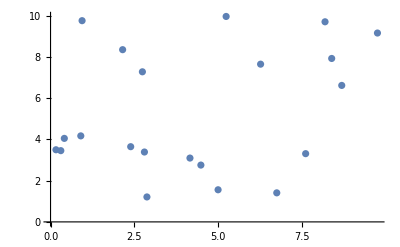

```mathematica
ListPlot[{{5.245648448676762,9.96105699043724},{0.9422194215635232,9.756737618709492},{8.200193903222216,9.702418246981743},{9.766355519383833,9.157784739128342},{2.1536571066854187,8.350604484827667},{8.399057539585852,7.9242768857252},{6.275109728138041,7.647953441862489},{2.7441332971616093,7.277680027086456},{8.699352152380465,6.617266996254577},{0.903848092170522,4.170504172451408},{0.4116264101092677,4.049217390246856},{2.39463834766666,3.6467899747304346},{0.30694321451698126,3.454619579680458},{0.1623151153434275,3.4975753150445708},{2.80473935776767,3.388151231274938},{7.620900973929286,3.308570079442476},{4.165069936280067,3.09514789952815},{4.491319444347757,2.755054746607773},{5.005118145646458,1.5577847391283406},{6.758274711303024,1.4085700794424767},{2.879486832515145,1.209617199861325}}]
```

```mathematica
Function[p,{(First[p]-originPoint[[1,1,1]])/xStep/4*2,(Last[p]-originPoint[[1,1,2]])/yStep/4*2}]/@points
```

```mathematica
{{5.245648448676762,9.96105699043724},{0.9422194215635232,9.756737618709492},{8.200193903222216,9.702418246981743},{9.766355519383833,9.157784739128342},{2.1536571066854187,8.350604484827667},{8.399057539585852,7.9242768857252},{6.275109728138041,7.647953441862489},{2.7441332971616093,7.277680027086456},{8.699352152380465,6.617266996254577},{0.903848092170522,4.170504172451408},{0.4116264101092677,4.049217390246856},{2.39463834766666,3.6467899747304346},{0.30694321451698126,3.454619579680458},{0.1623151153434275,3.4975753150445708},{2.80473935776767,3.388151231274938},{7.620900973929286,3.308570079442476},{4.165069936280067,3.09514789952815},{4.491319444347757,2.755054746607773},{5.005118145646458,1.5577847391283406},{6.758274711303024,1.4085700794424767},{2.879486832515145,1.209617199861325}}//TableForm
```

5.24565 | 9.96106
0.942219 | 9.75674
8.20019 | 9.70242
9.76636 | 9.15778
2.15366 | 8.3506
8.39906 | 7.92428
6.27511 | 7.64795
2.74413 | 7.27768
8.69935 | 6.61727
0.903848 | 4.1705
0.411626 | 4.04922
2.39464 | 3.64679
0.306943 | 3.45462
0.162315 | 3.49758
2.80474 | 3.38815
7.6209 | 3.30857
4.16507 | 3.09515
4.49132 | 2.75505
5.00512 | 1.55778
6.75827 | 1.40857
2.87949 | 1.20962

-Graphics-